### Power broadening

```mathematica
ϵ0=8.85*10^-12; c=3*10^8;A=(10^-6)^2;
ℏ=1.0545718*10^−34;
```

```mathematica
Δ=100; Γ=5;(*meV*)
τpulse=150*10^-15;τrep=1/(80*10^6);
d=10^-9*1.602*10^-19;
```

```mathematica
P0=100*10^-3;(*Watts*)
EField0=Sqrt[2*P0/(ϵ0*c*A)]*Sqrt[τrep/τpulse]; (*for peak power*)
Ω0=d*EField0/ℏ * (6.242*10^-15)  ;(*in meV*)
```

```mathematica
P1=10*10^-3;(*Watts*)
EField1=Sqrt[2*P1/(Pi*ϵ0*c*A)]*Sqrt[τrep/τpulse]; (*for peak power*)
Ω1=d*EField1/ℏ * (6.242*10^-15) ; (*in meV*)
```

```mathematica
P2=1*10^-3;(*Watts*)
EField2=Sqrt[2*P2/(Pi*ϵ0*c*A)]*Sqrt[τrep/τpulse]; (*for peak power*)
Ω2=d*EField2/ℏ * (6.242*10^-15);  (*in meV*)
```

```mathematica
P3=50*10^-3;(*Watts*)
EField3=Sqrt[2*P3/(Pi*ϵ0*c*A)]*Sqrt[τrep/τpulse]; (*for peak power*)
Ω3=d*EField3/ℏ * (6.242*10^-15) ; (*in meV*)
```

```mathematica
Pe[Δ_,Ω_,Γ_]:=(Ω^2/Γ^2)/(1+(2*Δ/Γ)^2+2*(Ω^2/Γ^2));
```

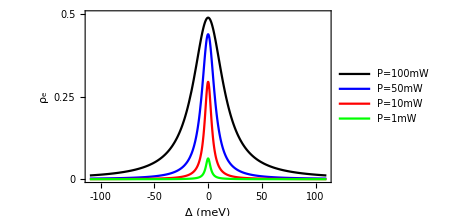

```mathematica
Plot[{Pe[Δ1,Ω0,Γ],Pe[Δ1,Ω3,Γ],Pe[Δ1,Ω1,Γ],Pe[Δ1,Ω2,Γ]},{Δ1,-110,110}, 
PlotRange->{Automatic,{0,0.5}},
Frame->True,
Axes->False,
FrameLabel->{"Δ (meV)", "ρ_e"},
FrameTicks->{{{0,0.25,0.5},None},{{-100,-50,0,50,100},None}},
FrameStyle->Directive[Black,20,FontFamily->"Cambria"],
FrameTicksStyle->Directive[Black,15,FontFamily->"Cambria"],
LabelStyle->Directive[Thick,Black,25,FontFamily->"Cambria"],
ImageSize->350,
PlotLegends->{"P=100mW","P=50mW","P=10mW","P=1mW"},
PlotStyle->{{Black},{Blue},{Red},{Green}}]
```